# Estados separables de 2 qubits

Las ideas principales en la búsqueda de estado separables son las siguientes:

Considerar un sistema de 2 qubits, el cual  está compuesto de dos subsistemas A y B, ambos de 1 qubit.  Además, se denotará como H_AB al espacio de Hilbert asociado a los estados del sistema completo AB.

Si se toman dos vectores ortonormales |v1⟩ , |v2⟩ que pertnecen a H_AB como base de un nuevo subespacio,  entonces los estados puros que pertenecen a este subespacio complejo bidimensional son de la forma  ψ =  A v1 + B v2, con A y B como coeficientes complejos.

En analogía con los estados puros de 1 qubit, se toman los coeficientes A = Cos(θ/2)  y  B = e^iϕSin(θ/2).

Para analizar la separabilidad de los estadosψ,  se hace uso de la pureza  γ_A = Tr [( ρ^A)^2], en donde ρ^A = Tr_B(ρ) y ρ  = ψψ.

Si γ_A=1, entonces el estado ψes separable.

Al ubicar los pares de valores { θ, ϕ } en donde γ_A=1, se encuentran a los estados ψ separables.

## Funciones

BaseStates[N, n]: retorna N vectores ortonormales complejos de dimensión 2^n.

PartialTrace[M, n]: calcula la traza parcial de M, de dimensión 4 x 4, sobre el n-ésimo qubit en la base computacional.

PurityOfSubsystemA[v1, v2, θ, ϕ]:  retorna el valor de la pureza γ_A = Tr [( ρ^A)^2] a partir de vectores base v1, v2 y  valores para θ, ϕ.

PointsWherePurityisMaximum[v1, v2]: retorna los pares de valores {θ, ϕ}, en donde γ_A es máxima, luego de recorrer el subespacio generado por v1 y v2.

```mathematica
BaseStates[N_,n_]:=Orthogonalize[Table[RandomComplex[],N,2^n]] (* Crea N listas con 2^n elementos complejos aleatorios, con valores entre 0 y 1*)
PartialTrace[M_,n_]:=Module[{M1}, 
M1=Partition[M,{2,2}]; (*particiona la lista M en bloques de 2x2*)
TensorContract[M1,Partition[Range[2^2],2][[n]]] (*para los elementos M1[[i,j,k,l]], contrae los índices i,j cuando n=1 y los índices k,l cuando n=2*)
]
PurityOfSubsystemA[v1_,v2_,θ_,ϕ_]:=Module[{ψ,ρ,ρA}, 
ψ=Cos[θ/2] v1+Exp[I ϕ] Sin[θ/2] v2; (*construye al vector ψ del subespacio generado por v1 y v2*)
ρ=Transpose[{ψ}].Conjugate[{ψ}]; (*construye la matriz densidad asociada al estado puro ψ*)
ρA=PartialTrace[ρ,2];(*traza parcial de ρ sobre el segundo qubit*)
Chop[FullSimplify[Tr[MatrixPower[ρA,2]],Element[{θ,ϕ},Reals]]] (*calcula el valor de la pureza para el estado ρA*)
]
PointsWherePurityisMaximum[v1_,v2_]:=Module[{M,dev,sol,d,data,secdθ,secdϕ,secdθϕ,delta,m,max,θ,ϕ},
(*calcula las primeras derivadas parciales de la pureza respecto de θ y ϕ*)
 dev={FullSimplify[Evaluate[D[PurityOfSubsystemA[v1,v2,θ,ϕ],θ] ,Element[{θ,ϕ},Reals]]],FullSimplify[Evaluate[D[PurityOfSubsystemA[v1,v2,θ,ϕ],ϕ] ,Element[{θ,ϕ},Reals]]]};
(*establece un límite superior para el valor de la pureza recorriendo todos los valores para θ y ϕ*)
M=NMaximize[{PurityOfSubsystemA[v1,v2,θ,ϕ],0≤θ≤π,0≤ϕ≤2 π},{θ,ϕ}][[1]];
(*Busca los puntos {θ,ϕ} donde la derivada es cero, empezando en {θ=θ0, ϕ=ϕ0}*)
sol[θ0_,ϕ0_]:={θ,ϕ}/.FindRoot[{dev[[1]]==0,dev[[2]]==0},{θ,θ0,0,Pi},{ϕ,ϕ0,0,2Pi}]; 
d=0.5; (* valor de los saltos entre los puntos {θ0} y {ϕ0}*)
(*Tabla con los valores {θ,ϕ} en donde la derivada es cero, para distintos puntos {θ0,ϕ0} de partida*)
data=Table[sol[θ0,ϕ0],{θ0,0,Pi,d},{ϕ0,0,2 Pi,0.5}]//Flatten[#,1]&//DeleteDuplicates@Chop[#]&//Quiet;
secdθ[θ_,ϕ_]:=Evaluate[D[PurityOfSubsystemA[v1,v2,θ,ϕ],{θ,2}]]; (*segunda derivada parcial en θ*)
     secdϕ[θ_,ϕ_]:=Evaluate[D[PurityOfSubsystemA[v1,v2,θ,ϕ],{ϕ,2}]] ; (* segunda derivada parcial en ϕ*)
     secdθϕ[θ_,ϕ_]:=Evaluate[D[PurityOfSubsystemA[v1,v2,θ,ϕ],{θ,1},{ϕ,1}]]; (* segunda derivada en θ,ϕ*)
     delta[θ_,ϕ_]:=secdθ[θ,ϕ] secdϕ[θ,ϕ]-secdθϕ[θ,ϕ]^2; (*determinante de la matriz Jacobiana*) 
(*selecciona los valores de {θ,ϕ} que cumplan con el criterio de la segunda derivada*)
m=Select[data,delta@@#>0&&secdθ@@#<0&];
(*Elimina puntos repetidos que tengan una diferencia menor a 10^-30 entre sí*)
max=DeleteDuplicates[m,Norm[#1-#2]<10^-13&] ;
(*elimina los puntos en la frontera y los que den un valor de pureza menor al límite M*)
DeleteCases[max,{x_,y_}/;0==y||y==2Pi|| PurityOfSubsystemA[v1,v2,x,y]<M]
]
```

## Pureza

### Vectores base v1 y v2

El primer paso es generar una base ortonormal para un sistema de 2 qubits:

```mathematica
Base=BaseStates[2,2];
v1=Base[[1]]
v2=Base[[2]]
```

{0.437513+0.299727 ⅈ,0.242221+0.16459 ⅈ,0.590786+0.478627 ⅈ,0.233965+0.0115784 ⅈ}

{0.0851977-0.103713 ⅈ,-0.181442+0.563157 ⅈ,-0.0861947-0.334662 ⅈ,0.652972+0.293456 ⅈ}

### Gráficas

Con la base lista, puede visualizarse la base sobre una esfera:

```mathematica
y=Image[DensityPlot[PurityOfSubsystemA[v1,v2,θ,ϕ]//Evaluate,{θ,0,π},{ϕ,0,2 π},ColorFunction->"Rainbow",Frame->False,ImagePadding->None,PerformanceGoal->"Quality",PlotPoints->55,PlotRange->All,PlotRangePadding->None],ImageResolution->144];
ParametricPlot3D[{Cos[ϕ] Sin[θ],Sin[ϕ] Sin[θ],Cos[θ]},{θ,0,π},{ϕ,0,2 π},Lighting->"Neutral",Mesh->None ,PlotStyle->Texture[y],LabelStyle->{FontSize->14},AxesLabel->{Style["x axis",16,Bold,Black],Style["y axis",16,Bold,Black],Style["z axis",16,Bold,Black]},ImageSize->Large,   PlotLegends->BarLegend[{"Rainbow",{NMinimize[{PurityOfSubsystemA[v1,v2,θ,ϕ],0≤θ≤π,0≤ϕ≤2 π},{θ,ϕ}][[1]],NMaximize[{PurityOfSubsystemA[v1,v2,θ,ϕ],0≤θ≤π,0≤ϕ≤2 π},{θ,ϕ}][[1]]}},LabelStyle->{Black,FontSize-> 10}]]
```

-Graphics3D-

## Máximos

### Puntos θ, ϕ

Ahora, se localizan los pares de valores {θ, ϕ} en donde la pureza es máxima:

```mathematica
maximos=PointsWherePurityisMaximum[v1,v2]
```

{{0.474306,1.60714},{2.70619,6.05698}}

### Gráficas con máximos

Los puntos máximos pueden visualizarse en un mapa de contorno . En este caso se representan como puntos blancos.

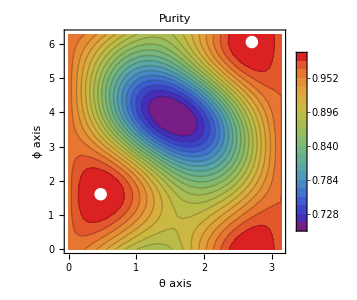

```mathematica
ContourPlot[PurityOfSubsystemA[v1,v2,θ,ϕ],{θ,0,Pi},{ϕ,0,2 Pi},ColorFunction->"Rainbow",Contours->20,ContourStyle->Opacity[.2],PlotLegends->Automatic,ImageSize->300,FrameLabel->{Style["θ axis",15,Bold,Black],Style["ϕ axis",15,Bold,Black]},Epilog->{White,PointSize[0.03],Point[maximos]},PlotLabel->Style["Purity",15,Bold,Black]]
```

### Confirmando pureza

Es de interés ubicar los valores donde γ_A=1, por lo que puede verificarse al sustituir los  pares de θ  y  ϕ  encontrados.

```mathematica
PurityOfSubsystemA[v1,v2,maximos[[1,1]],maximos[[1,2]]]
PurityOfSubsystemA[v1,v2,maximos[[2,1]],maximos[[2,2]]]
```

1.

1.

## Componentes de los estados separables

Finalmente, pueden encontrarse las componentes de los estados separables  al sustituir los valores de θ  y ϕ  en  ψ=Cos(θ/2) v1 + e^(i ϕ) Sin(θ/2) v2.

```mathematica
θ1=maximos[[1,1]];θ2=maximos[[2,1]];ϕ1=maximos[[1,2]];ϕ2=maximos[[2,2]];
ψ1=Cos[θ1/2] v1+Exp[I ϕ1] Sin[θ1/2] v2
ψ2=Cos[θ2/2] v1+Exp[I ϕ2] Sin[θ2/2] v2
```

{0.44889+0.312226 ⅈ,0.104772+0.112576 ⅈ,0.653558+0.447851 ⅈ,0.152944+0.162055 ⅈ}

{0.152851-0.0526066 ⅈ,0.00299592+0.611139 ⅈ,-0.0277034-0.196187 ⅈ,0.736114+0.138737 ⅈ}